# Notebook for : Kerr Orbit Visualization

Geoff Cope
University of Utah
April 26th, 2021

```mathematica
(*
Just a slight modification of Maarten van de Meent's notebook linked below
*)
```

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<KerrGeodesics`
```

## Hyperlink to BHPToolkit Spring 2020 Workshop - See Monday May 25 15:15-16:00 Maarten van de Meent

```mathematica
Hyperlink["BHPToolkit Spring 2020 Workshop - See Monday May 25 15:15-16:00 Maarten van de Meent",
"https://astro.cas.cz/bhptoolkit2020/program.html"]
```

[BHPToolkit Spring 2020 Workshop - See Monday May 25 15:15-16:00 Maarten van de Meent](https://astro.cas.cz/bhptoolkit2020/program.html)

## Find All Crossings Link

```mathematica
Hyperlink["FindAllCrossings Link",
"https://mathematica.stackexchange.com/questions/5663/about-multi-root-search-in-mathematica-for-transcendental-equations/5666#5666"]
```

[FindAllCrossings Link](https://mathematica.stackexchange.com/questions/5663/about-multi-root-search-in-mathematica-for-transcendental-equations/5666#5666)

```mathematica
Options[FindAllCrossings]=Sort[Join[Options[FindRoot],{MaxRecursion->Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints->Automatic}]];

FindAllCrossings[f_,{t_,a_,b_},opts___]:=Module[{r,s,s1,ya},{r,ya}=Transpose[First[Cases[Normal[Plot[f,{t,a,b},Method->Automatic,Evaluate[Sequence@@FilterRules[Join[{opts},Options[FindAllCrossings]],Options[Plot]]]]],Line[l_]:>l,Infinity]]];
s1=Sign[ya];If[!MemberQ[Abs[s1],1],Return[{}]];
s=Times@@@Partition[s1,2,1];
If[MemberQ[s,-1]||MemberQ[Take[s,{2,-2}],0],Union[Join[Pick[r,s1,0],Select[t/. Map[FindRoot[f,{t,r[[#]],r[[#+1]]},Evaluate[Sequence@@FilterRules[Join[{opts},Options[FindAllCrossings]],Options[FindRoot]]]]&,Flatten[Position[s,-1]]],a<=#<=b&]]],{}]]  ;
```

```mathematica
Clear[orbitVisualization]
orbitVisualization[𝒶_,p_,e_,𝓍_,lambdaMax_]:=  
(* a appears in FindAllCrossings, just use [esc]sca[esc] for 𝒶 *) 
(* x appears as the x coordinate and as the parameter x in Kerr Geodesics , be careful , we use [esc]scx[esc] here  *) 
Module[{} ,

Clear[orbit]  ; 
orbit = 
KerrGeoOrbit[𝒶,p,e,𝓍] ;
 
Clear[t] ;
t = orbit[λ][[1]] ;

Clear[tPlot] ; 
tPlot = 
 Plot[ t , {λ,0, lambdaMax },AxesLabel-> { "λ" , orbit["Parametrization"] }  ]  ; 


Clear[𝓇] ; 
𝓇  = orbit[λ][[2]] ;

Clear[rPlot] ; 
rPlot = Plot[ 𝓇 , {λ,0,lambdaMax},AxesLabel-> { "λ" ,"r"}   ]   ; 

Clear[θ] ; 
θ = orbit[λ][[3]] ;

Clear[thetaPlot] ;
thetaPlot = Plot[ θ , {λ,0,lambdaMax} ,AxesLabel-> { "λ" ,"θ"}]  ;

Clear[ϕ] ; 
ϕ = orbit[λ][[4]] ; 

Clear[phiPlot] ;
 phiPlot = Plot[ϕ, {λ,0,lambdaMax} ,AxesLabel-> { "λ" ,"ϕ"} ]  ; 

Clear[x] ; 
x = 𝓇 Cos[ϕ]Sin[θ] ; 

Clear[xPlot] ; 
xPlot = 
Plot[ x, {λ,0,lambdaMax},AxesLabel-> { "λ" ,"x"}  ]  ; 

Clear[y] ; 
y = 𝓇 Sin[ϕ]Sin[θ] ; 

Clear[yPlot] ; 
yPlot = 
Plot[ y, {λ,0,lambdaMax},AxesLabel-> { "λ" ,"y"} ]  ; 

Clear[z] ; 
z = 𝓇 Cos[θ]  ; 

Clear[zPlot] ; 
zPlot = 
Plot[ z, {λ,0,lambdaMax},AxesLabel-> { "λ" ,"z"} ]  ; 

Clear[yzPlaneCrossings] ; 
yzPlaneCrossings = 
FindAllCrossings[ x ,  {λ,0,lambdaMax}] ;

Clear[yzPlaneCoordinates] ; 
yzPlaneCoordinates = 
Table[
{ y  /. λ-> yzPlaneCrossings[[i]]  , z  /. λ-> yzPlaneCrossings[[i]]  } 
, { i , 1 , Length[ yzPlaneCrossings] } ]  ;

Clear[yzCrossSection] ;
yzCrossSection = 
ListPlot[ yzPlaneCoordinates ,PlotLabel-> "y-z Plane" ]  ; 

Clear[xzPlaneCrossings] ; 
xzPlaneCrossings = 
FindAllCrossings[ y ,  {λ,0,lambdaMax}] ;

Clear[xzPlaneCoordinates] ; 
xzPlaneCoordinates = 
Table[
{ x  /. λ-> xzPlaneCrossings[[i]]  , z  /. λ-> xzPlaneCrossings[[i]]  } 
, { i , 1 , Length[ xzPlaneCrossings] } ]  ;

Clear[xzCrossSection] ;
xzCrossSection = 
ListPlot[ xzPlaneCoordinates ,PlotLabel-> "x-z Plane" ]  ; 

Clear[xyPlaneCrossings] ; 
xyPlaneCrossings = 
FindAllCrossings[ z ,  {λ,0,lambdaMax}] ;

Clear[xyPlaneCoordinates] ; 
xyPlaneCoordinates = 
Table[
{ x  /. λ-> xyPlaneCrossings[[i]]  , y  /. λ-> xyPlaneCrossings[[i]]  } 
, { i , 1 , Length[ xyPlaneCrossings] } ]  ;

Clear[xyCrossSection] ;
xyCrossSection = 
ListPlot[ xyPlaneCoordinates,PlotLabel-> "x-y Plane"   ]  ; 


Clear[allPlots] ;
allPlots = { tPlot  , rPlot  , thetaPlot  ,  phiPlot , xPlot, yPlot, zPlot ,  yzCrossSection,xzCrossSection,xyCrossSection   } ;

Table[allPlots[[i]]   , {i, 1 , Length[ allPlots]} ]  // TableForm
]
```

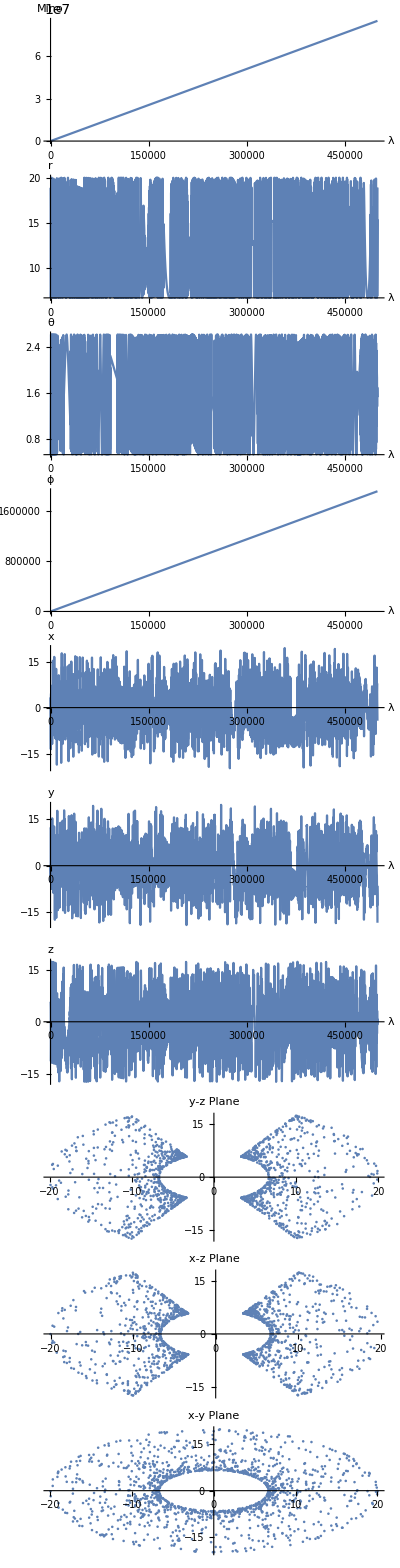

```mathematica
orbitVisualization[0.9 , 10.0 , 0.5 , 0.5,500000]
```

```mathematica
Clear[orbit]
orbit = 
KerrGeoOrbit[0.9 , 10.0 , 0.5 , 0.5 ]
```

KerrGeoOrbitFunction[…]

```mathematica
Manipulate[
Module[
{to,ro,θo,ϕo,λ,Λr},
{to,ro,θo,ϕo}=orbit[λ];
Λr=2π/orbit["RadialFrequency"];
Show[
ParametricPlot3D[
ro{Cos[ϕo]Sin[θo],Sin[ϕo]Sin[θo],Cos[θo]},{λ,0,(orbits) Λr}
,Lighting->"Neutral",PlotPoints->200,PlotRange->20 , ImageSize-> Large  , AxesLabel->{"x","y","z"}],
Graphics3D[{Black,Specularity[.5],Sphere[{0,0,0},1+√(1-(.9)^2)]}]
]
] , 
{orbits, 1, 200 } ]
```

```mathematica
Clear[kerrInformation]
kerrInformation[𝒶_,p_,e_,𝓍_]:= { 
Print["KerrGeoEnergy is: "  ,  KerrGeoEnergy[𝒶,p,e,𝓍] ]  , 
Print["KerrGeoAngularMomentum is: ",KerrGeoAngularMomentum[𝒶,p,e,𝓍] ], 
Print["KerrGeoCarterConstant is: " , KerrGeoCarterConstant[𝒶,p,e,𝓍] ], 
Print["KerrGeoConstantsOfMotion: ",KerrGeoConstantsOfMotion[𝒶,p,e,𝓍] ], 
Print["KerrGeoFrequencies are: " , KerrGeoFrequencies[𝒶,p,e,𝓍]] , 
Print["KerrGeoBoundOrbitQ is: " KerrGeoBoundOrbitQ[𝒶,p,e,𝓍] ]  , 
Print[ "KerrGeoPhotonSphereRadius is: " , KerrGeoPhotonSphereRadius[𝒶,𝓍]] , 
Print["KerrGeoISCO is: ",KerrGeoISCO[𝒶,𝓍]] , 
Print["KerrGeoISBO is: " KerrGeoISBO[𝒶,𝓍] ], 
Print["KerrGeoISSO is: ", KerrGeoISSO[𝒶,𝓍] ], 
Print["KerrGeoSeparatrix is: " , KerrGeoSeparatrix[𝒶,e,𝓍]] , 
Print["KerrGeoOrbit is: " ,  KerrGeoOrbit[𝒶,p,e,𝓍]]
} ;
```

```mathematica
Clear[test1]
test1 = 
kerrInformation[0.9,10,0.5,0.5]
```

KerrGeoEnergy is: 0.964707

KerrGeoAngularMomentum is: 1.81884

KerrGeoCarterConstant is: 9.96668

KerrGeoConstantsOfMotion: <|ℰ→0.964707,ℒ→1.81884,𝒬→9.96668|>

KerrGeoFrequencies are: <|Ω_r→0.015827,Ω_θ→0.0213672,Ω_ϕ→0.0225415|>

KerrGeoBoundOrbitQ is:  True

KerrGeoPhotonSphereRadius is: 1.9291

KerrGeoISCO is: KerrGeoISCO[0.9,0.5]

KerrGeoISBO is:  KerrGeoISBO[0.9,0.5]

KerrGeoISSO is: 3.73286

KerrGeoSeparatrix is: 4.34226

KerrGeoOrbit is: KerrGeoOrbitFunction[…]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
kerrInformation[0.92,10,0.5,0.5]
```

KerrGeoEnergy is: 0.964679

KerrGeoAngularMomentum is: 1.81651

KerrGeoCarterConstant is: 9.94318

KerrGeoConstantsOfMotion: <|ℰ→0.964679,ℒ→1.81651,𝒬→9.94318|>

KerrGeoFrequencies are: <|Ω_r→0.015854,Ω_θ→0.0213302,Ω_ϕ→0.0225254|>

KerrGeoBoundOrbitQ is:  True

KerrGeoPhotonSphereRadius is: 1.87066

KerrGeoISCO is: KerrGeoISCO[0.92,0.5]

KerrGeoISBO is:  KerrGeoISBO[0.92,0.5]

KerrGeoISSO is: 3.63856

KerrGeoSeparatrix is: 4.22717

KerrGeoOrbit is: KerrGeoOrbitFunction[…]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
orbit[[1]]
```

0.9